```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s2/Documents/Wolfram Mathematica

```mathematica
raw = Import["/home/s2/Projects-CUDA/build-iceMPM_3Dm-Desktop_Qt_5_15_2_GCC_64bit-Release/_output/indenter.h5","IndenterTotals"];
```

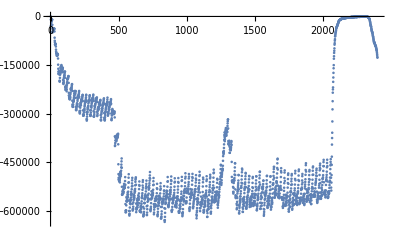

```mathematica
ListPlot[raw[[1;;-1,2]]]
```

```mathematica
tval=raw⟦1;;-1,1⟧;
```

```mathematica
fval=raw[[1;;-1,5]]/1000;
```

```mathematica
Max[fval]//N
```

1026.75

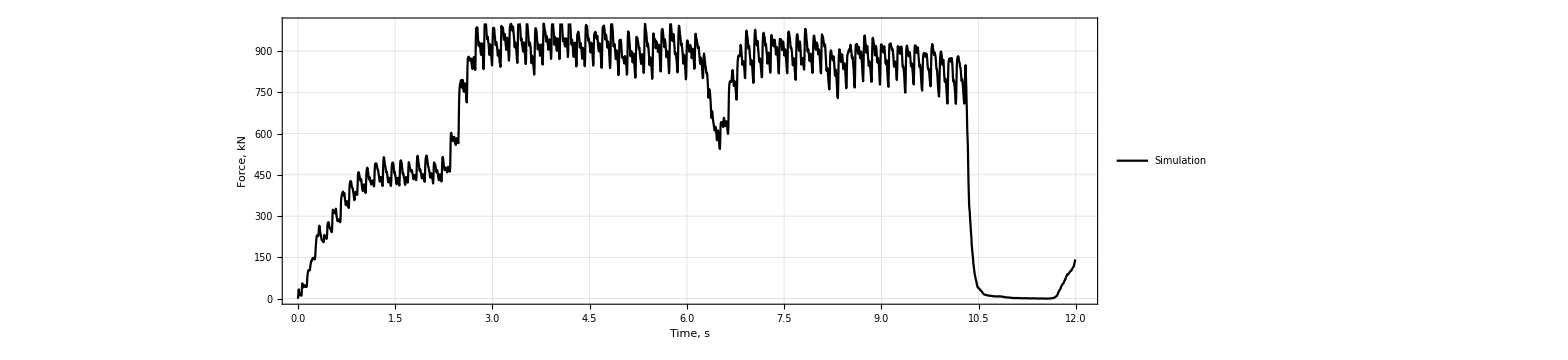

```mathematica
forceplot=ListLinePlot[Transpose[{tval,fval}],PlotTheme->"Detailed",AspectRatio->0.3,ImageSize->1200,FrameLabel->{{"Force, kN",""},{"Time, s",""}},PlotStyle->{{Thick,Black}},BaseStyle->{FontSize->25,FontFamily->"Times New Roman"},FrameStyle->Directive[Black],PlotRange->{{0,tval[[-1]]+0.1},{0,1000}},PlotLegends->{Style["Simulation",25,FontFamily->"Times New Roman"]}]
```

```mathematica
Export["force_plot.png",forceplot]
```

force_plot.png